```mathematica
RSolve[{a[n]==2a[n/2] + n Log[2,n], a[1]==1} ,a[n],n]
RSolve[{a[n]==2 a[n-1]+2^n * n, a[0]==1},a[n],n]
RSolve[{a[n]==a[Sqrt[n]] + Log[2,n], a[1]==1} ,a[n],n]
```

{{a[n]→(n (Log[4]-2 Log[n^(1/2 (-1-Log[n]/Log[2]))]))/Log[4]}}

{{a[n]→2^(-1+n) (2+n+n^2)}}

{{a[n]→(Log[2]+2 Log[n])/Log[2]}}

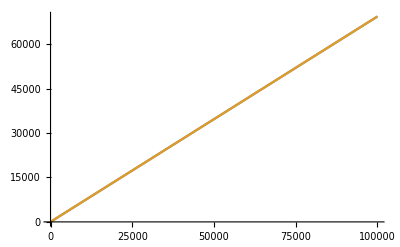

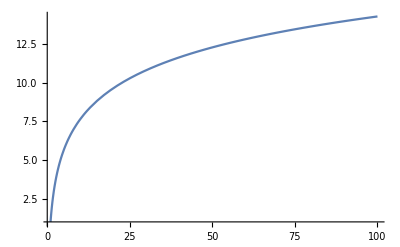

$Aborted

-Graphics-

```mathematica
Plot[{2^(-1+n) (2+n+n^2)//Log,2^n * n//Log}, {n,1,100000}]
Plot[(Log[2]+2 Log[n])/Log[2],{n,1,100}]
```

```mathematica
(n (Log[4]-2 Log[n^(1/2 (-1-Log[n]/Log[2]))]))/Log[4]//FullSimplify
```

n-(2 n Log[n^(-Log[2 n]/Log[4])])/Log[4]

```mathematica
(Log[2]+2 Log[n])/Log[2]//FullSimplify
```

1+(2 Log[n])/Log[2]

```mathematica
f[n_]:=1 + Log[2, n^2];
f[n] - f[Sqrt[n]] - Log[2,n]//FullSimplify
```

(-2 Log[n]+Log[n^2])/Log[2]

```mathematica
Log[5^2]-2Log[5]//N
```

0.